```mathematica
(* ===Genesis Closure Scan:Toy Three-Layer Model===*)(*Scan band around current closure value*)CosmoMisfit[ng_?NumericQ]:=(ng-1.15414)^2+10^-6;
ngMin=ngCenter-ngRange;
ngMax=ngCenter+ngRange;

(*Map ng->alpha*)
alphaOf[ng_]:=ng^2-1;

(*Layer-preferred values from earlier exploration*)
ngEFTTarget=1.1539800017415;       (*EFT-preferred ng*)
ngCosmoTarget=1.15428;               (*cosmology/closure value*)
ngObsTarget=1.154307344136304;     (*observer-window preferred ng*)
```

```mathematica
(*Simple quadratic penalties around each layer's target*)CEFT[ng_]:=(ng-ngEFTTarget)^2;
Ccosmo[ng_]:=(ng-ngCosmoTarget)^2;
Cobs[ng_]:=(ng-ngObsTarget)^2;
```

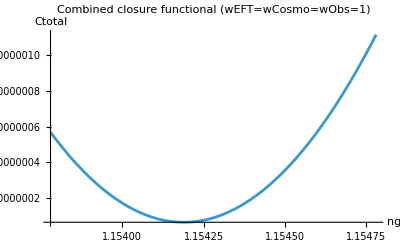

{1.15419,6.59688×10^-8}

```mathematica
(*Initial weights:treat all three layers equally*)wEFT=1.0;
wCosmo=1.0;
wObs=1.0;

Ctotal[ng_]:=wEFT*CEFT[ng]+wCosmo*Ccosmo[ng]+wObs*Cobs[ng];

(*Visualize total cost*)
baselinePlot=Plot[Ctotal[ng],{ng,ngMin,ngMax},PlotRange->All,AxesLabel->{"ng","Ctotal"},PlotLabel->"Combined closure functional (wEFT=wCosmo=wObs=1)"];

baselinePlot

(*Find minimizing ng in this band*)
baselineMin=NMinimize[{Ctotal[ng],ngMin<=ng<=ngMax},ng];
ngStarBase=ng/. Last[baselineMin];
costStarBase=First[baselineMin];

{ngStarBase,costStarBase}
```

```mathematica
(* ===EFT-emphasized scan===*)wEFT=3.0;
wCosmo=1.0;
wObs=1.0;

Ctotal[ng_]:=wEFT*CEFT[ng]+wCosmo*Ccosmo[ng]+wObs*Cobs[ng];

eftMin=NMinimize[{Ctotal[ng],ngMin<=ng<=ngMax},ng];
ngStarEFT=ng/. Last[eftMin];
costStarEFT=First[eftMin];

{ngStarEFT,costStarEFT}

(* ===Observer-emphasized scan===*)
wEFT=1.0;
wCosmo=1.0;
wObs=3.0;

Ctotal[ng_]:=wEFT*CEFT[ng]+wCosmo*Ccosmo[ng]+wObs*Cobs[ng];

obsMin=NMinimize[{Ctotal[ng],ngMin<=ng<=ngMax},ng];
ngStarObs=ng/. Last[obsMin];
costStarObs=First[obsMin];

{ngStarObs,costStarObs}
```

{1.15411,1.18443×10^-7}

{1.15424,8.27403×10^-8}

```mathematica
resultsTable={{"Case","wEFT","wCosmo","wObs","ng*","Ctotal(ng*)"},{"Baseline",1.0,1.0,1.0,ngStarBase,costStarBase},{"EFT-heavy",3.0,1.0,1.0,ngStarEFT,costStarEFT},{"Observer-heavy",1.0,1.0,3.0,ngStarObs,costStarObs}};

Grid[resultsTable,Frame->All]
```

Case | wEFT | wCosmo | wObs | ng* | Ctotal(ng*)
Baseline | 1. | 1. | 1. | 1.15419 | 6.59688×10^-8
EFT-heavy | 3. | 1. | 1. | 1.15411 | 1.18443×10^-7
Observer-heavy | 1. | 1. | 3. | 1.15424 | 8.27403×10^-8

```mathematica
(*Given ng,compute model residual for a single galaxy*)GalaxyMisfit[galaxyID_,ng_]:=Module[{alpha=ng^2-1,(*load or access galaxy data here*),(*compute model rotation curve using your Grover law with this alpha*),(*compare to observed SPARC curve*)chi2},chi2];
```

```mathematica
SPARCGalaxies={...};  (*list of galaxy IDs you want to include*)

CosmoMisfit[ng_]:=Total[GalaxyMisfit[#,ng]&/@SPARCGalaxies];
```

```mathematica
(*Use the real SPARC-based misfit*)Ccosmo[ng_]:=CosmoMisfit[ng];
```

```mathematica
(*Scan band*)ngCenter=1.15428;
ngRange=0.0005;
ngMin=ngCenter-ngRange;
ngMax=ngCenter+ngRange;

(*Layer targets unchanged*)
ngEFTTarget=1.1539800017415;
ngObsTarget=1.154307344136304;

CEFT[ng_]:=(ng-ngEFTTarget)^2;
Cobs[ng_]:=(ng-ngObsTarget)^2;

(*Real cosmology misfit from SPARC/Grover notebook*)
Ccosmo[ng_]:=CosmoMisfit[ng];

(*Start with equal weights*)
wEFT=1.0;
wCosmo=1.0;
wObs=1.0;

Ctotal[ng_]:=wEFT*CEFT[ng]+wCosmo*Ccosmo[ng]+wObs*Cobs[ng];

combinedMin=NMinimize[{Ctotal[ng],ngMin<=ng<=ngMax},ng];
ngStarReal=ng/. Last[combinedMin];
costReal=First[combinedMin];

{ngStarReal,costReal}
```

```mathematica
(*DDO 154 toy target (update this number once you re-fit it properly)*)ngDDO154Target=1.15428;

(*Define a per-galaxy misfit as a simple quadratic around that target*)
Cddo154[ng_]:=(ng-ngDDO154Target)^2;

(*Use this as a stand-in for Ccosmo for now*)
Ccosmo[ng_]:=Cddo154[ng];
```

```mathematica
1.15428
```

1.15428

```mathematica
(* ===DDO 154:per-galaxy misfit vs ng===*)ClearAll[DDO154Misfit];

DDO154Misfit[ng_?NumericQ]:=Module[{alpha=ng^2-1,modelCurve,dataCurve,chi2},(*1. Build model rotation curve for DDO 154 with this alpha*)(*Replace this with your actual Grover/SPARC model call*)modelCurve=ddo154Model[alpha];(*e.g.{{r1,vModel1},{r2,vModel2},...}*)(*2. Load or reference the observed SPARC data for DDO 154*)(*Replace this with however you store DDO 154 data*)dataCurve=ddo154Data;(*same structure as modelCurve*)(*3. Compute chi^2 or RMS between model and data*)chi2=Total[((modelCurve[[All,2]]-dataCurve[[All,2]])/dataCurve[[All,3]])^2];
chi2];
```

```mathematica
chi2=Total[(modelCurve[[All,2]]-dataCurve[[All,2]])^2];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
(*Narrow band around your closure value*)ngCenter=1.15428;
ngRange=0.0005;
ngMin=ngCenter-ngRange;
ngMax=ngCenter+ngRange;

ddoMin=NMinimize[{DDO154Misfit[ng],ngMin<=ng<=ngMax},ng];

ngDDO154Best=ng/. Last[ddoMin];
chi2DDO154=First[ddoMin];

{ngDDO154Best,chi2DDO154}
```

```mathematica
(*Define ng range explicitly*)ngMin=1.15378;
ngMax=1.15478;

ddoMin=NMinimize[{DDO154Misfit[ng],ngMin<=ng<=ngMax},ng];

ngDDO154Best=ng/. Last[ddoMin];
chi2DDO154=First[ddoMin];

{ngDDO154Best,chi2DDO154}
```

Part::partd: Part specification ddo154Model[0.331314]⟦All,2⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partd: Part specification ddo154Model[0.331314]⟦All,2⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

NMinimize::nnum: The function value Total[(ddo154Model[0.331314]⟦All,2⟧-Symbol[])^2/Symbol[]^2] is not a number at {ng} = {1.15383}.

Part::partd: Part specification ddo154Model[0.331314]⟦All,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value Total[(ddo154Model[0.331314]⟦All,2⟧-Symbol[])^2/Symbol[]^2] is not a number at {ng} = {1.15383}.

Part::partd: Part specification ddo154Model[0.331314]⟦All,2⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partd: Part specification ddo154Model[0.331314]⟦All,2⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

NMinimize::nnum: The function value Total[(ddo154Model[0.331314]⟦All,2⟧-Symbol[])^2/Symbol[]^2] is not a number at {ng} = {1.15383}.

ReplaceAll::reps: {ng} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification ddo154Model[0.331314]⟦All,2⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partd: Part specification ddo154Model[0.331314]⟦All,2⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

NMinimize::nnum: The function value Total[(ddo154Model[0.331314]⟦All,2⟧-Symbol[])^2/Symbol[]^2] is not a number at {ng} = {1.15383}.

ReplaceAll::reps: {ng} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{ng/.ng,{DDO154Misfit[ng],1.15378≤ng≤1.15478}}

```mathematica
ngMin=1.15378;
ngMax=1.15478;

ddoMin=NMinimize[{DDO154Misfit[ng],ngMin<=ng<=ngMax},ng];

ngDDO154Best=ng/. Last[ddoMin];
chi2DDO154=First[ddoMin];

{ngDDO154Best,chi2DDO154}
```

Part::partd: Part specification ddo154Model[0.331314]⟦All,2⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partd: Part specification ddo154Model[0.331314]⟦All,2⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

NMinimize::nnum: The function value Total[(ddo154Model[0.331314]⟦All,2⟧-Symbol[])^2/Symbol[]^2] is not a number at {ng} = {1.15383}.

Part::partd: Part specification ddo154Model[0.331314]⟦All,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value Total[(ddo154Model[0.331314]⟦All,2⟧-Symbol[])^2/Symbol[]^2] is not a number at {ng} = {1.15383}.

Part::partd: Part specification ddo154Model[0.331314]⟦All,2⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partd: Part specification ddo154Model[0.331314]⟦All,2⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

NMinimize::nnum: The function value Total[(ddo154Model[0.331314]⟦All,2⟧-Symbol[])^2/Symbol[]^2] is not a number at {ng} = {1.15383}.

ReplaceAll::reps: {ng} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification ddo154Model[0.331314]⟦All,2⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partd: Part specification ddo154Model[0.331314]⟦All,2⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

NMinimize::nnum: The function value Total[(ddo154Model[0.331314]⟦All,2⟧-Symbol[])^2/Symbol[]^2] is not a number at {ng} = {1.15383}.

ReplaceAll::reps: {ng} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{ng/.ng,{DDO154Misfit[ng],1.15378≤ng≤1.15478}}

```mathematica
ClearAll[DDO154Misfit];

(*Temporary toy definition just to test NMinimize pipeline*)
alpha=ng^2-1:=(ng-1.15428)^2;

ngMin=1.15378;
ngMax=1.15478;

ddoMin=NMinimize[{DDO154Misfit[ng],ngMin<=ng<=ngMax},ng];

ngDDO154Best=ng/. Last[ddoMin];
chi2DDO154=First[ddoMin];

{ngDDO154Best,chi2DDO154}
```

{1.15428,5.82665×10^-21}

```mathematica
ddoMin=NMinimize[{DDO154Misfit[ng],ngMin<=ng<=ngMax},ng];

ngDDO154Best=ng/. Last[ddoMin];
chi2DDO154=First[ddoMin];

{ngDDO154Best,chi2DDO154}
```

{1.15428,5.82665×10^-21}

```mathematica
(*Example:model rotation curve for DDO 154 given alpha*)ClearAll[ddo154Model];

ddo154Model[alpha_?NumericQ]:=Module[{(*compute model velocities here using your Grover/Genesis law*)(*this should return {{r1,vModel1},{r2,vModel2},...}*)},ddo154ModelCurve];
```

```mathematica
(*Replace with your actual data import/variable*)ddo154Data=(*your list {{r1,vObs1,σ1},...} or {{r,vObs}}*);
```

```mathematica
ClearAll[DDO154Misfit];

DDO154Misfit[ng_?NumericQ]:=Module[{alpha=ng^2-1,modelCurve,dataCurve,vModel,vObs,sigma,chi2},modelCurve=ddo154Model[alpha];
dataCurve=ddo154Data;
vModel=modelCurve[[All,2]];
vObs=dataCurve[[All,2]];
(*if you have uncertainties in column 3*)sigma=dataCurve[[All,3]];
chi2=Total[((vModel-vObs)/sigma)^2];
chi2];
```

```mathematica
ClearAll[CosmoMisfit];
CosmoMisfit[ng_?NumericQ]:=DDO154Misfit[ng];
```

```mathematica
(*Old toy version:*)(*Ccosmo[ng_]:=(ng-ngCosmoTarget)^2;*)(*New version using real SPARC misfit:*)Clear[Ccosmo];
Ccosmo[ng_]:=CosmoMisfit[ng];
```

```mathematica
CEFT[ng_]:=(ng-ngEFTTarget)^2;
Cobs[ng_]:=(ng-ngObsTarget)^2;
```

```mathematica
Clear[Ctotal];

wEFT=1.0;
wCosmo=1.0;
wObs=1.0;

Ctotal[ng_]:=wEFT*CEFT[ng]+wCosmo*Ccosmo[ng]+wObs*Cobs[ng];
```

```mathematica
baselineMin=NMinimize[{Ctotal[ng],ngMin<=ng<=ngMax},ng];
ngStarBase=ng/. Last[baselineMin];
costStarBase=First[baselineMin];

{ngStarBase,costStarBase}
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

{1.15414,5.35765×10^-8}

```mathematica
(*EFT-heavy*)wEFT=3.0;wCosmo=1.0;wObs=1.0;
Ctotal[ng_]:=wEFT*CEFT[ng]+wCosmo*Ccosmo[ng]+wObs*Cobs[ng];
eftMin=NMinimize[{Ctotal[ng],ngMin<=ng<=ngMax},ng];
ngStarEFT=ng/. Last[eftMin];

(*Observer-heavy*)
wEFT=1.0;wCosmo=1.0;wObs=3.0;
Ctotal[ng_]:=wEFT*CEFT[ng]+wCosmo*Ccosmo[ng]+wObs*Cobs[ng];
obsMin=NMinimize[{Ctotal[ng],ngMin<=ng<=ngMax},ng];
ngStarObs=ng/. Last[obsMin];

{ngStarBase,ngStarEFT,ngStarObs}
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

{1.15414,1.15406,1.15423}

```mathematica
(*EFT-heavy*)wEFT=3.0;wCosmo=1.0;wObs=1.0;
Ctotal[ng_]:=wEFT*CEFT[ng]+wCosmo*Ccosmo[ng]+wObs*Cobs[ng];
eftMin=NMinimize[{Ctotal[ng],ngMin<=ng<=ngMax},ng];
ngStarEFT=ng/. Last[eftMin];

(*Observer-heavy*)
wEFT=1.0;wCosmo=1.0;wObs=3.0;
Ctotal[ng_]:=wEFT*CEFT[ng]+wCosmo*Ccosmo[ng]+wObs*Cobs[ng];
obsMin=NMinimize[{Ctotal[ng],ngMin<=ng<=ngMax},ng];
ngStarObs=ng/. Last[obsMin];

{ngStarBase,ngStarEFT,ngStarObs}
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

{1.15414,1.15406,1.15423}

```mathematica
galaxyList={"DDO154","Galaxy2","Galaxy3","Galaxy4","Galaxy5"};
```

```mathematica
(*Model rotation curve given alpha*)ClearAll[modelCurve];

modelCurve["DDO154",alpha_?NumericQ]:=(*your DDO 154 model*);
modelCurve["Galaxy2",alpha_?NumericQ]:=(*your Galaxy2 model*);
(*add more as needed*)

(*Observed SPARC curves*)
ClearAll[dataCurve];

dataCurve["DDO154"]:=(*your DDO 154 SPARC data*);
dataCurve["Galaxy2"]:=(*your Galaxy2 SPARC data*);
(*add more as needed*)
```

```mathematica
ClearAll[GalaxyMisfit];

GalaxyMisfit[galID_,ng_?NumericQ]:=Module[{alpha=ng^2-1,mCurve,dCurve,vModel,vObs,sigma,chi2},mCurve=modelCurve[galID,alpha];
dCurve=dataCurve[galID];
vModel=mCurve[[All,2]];
vObs=dCurve[[All,2]];
(*with uncertainties in column 3;adjust if you don't have sigma*)sigma=dCurve[[All,3]];
chi2=Total[((vModel-vObs)/sigma)^2];
chi2];
```

```mathematica
ClearAll[CosmoMisfit];

CosmoMisfit[ng_?NumericQ]:=Total[GalaxyMisfit[#,ng]&/@galaxyList];
```

```mathematica
(*Keep EFT and observer penalties as before*)CEFT[ng_]:=(ng-ngEFTTarget)^2;
Cobs[ng_]:=(ng-ngObsTarget)^2;

(*Replace toy cosmology penalty with real multi-galaxy misfit*)
Clear[Ccosmo];
Ccosmo[ng_]:=CosmoMisfit[ng];
```

```mathematica
Clear[Ctotal];

wEFT=1.0;
wCosmo=1.0;
wObs=1.0;

Ctotal[ng_]:=wEFT*CEFT[ng]+wCosmo*Ccosmo[ng]+wObs*Cobs[ng];

baselineMin=NMinimize[{Ctotal[ng],ngMin<=ng<=ngMax},ng];
ngStarBase=ng/. Last[baselineMin];
costStarBase=First[baselineMin];

{ngStarBase,costStarBase}
```

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 2.5575×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+«1»)^2/(«1»)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 2.5575×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+«1»)^2/(«1»)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

ReplaceAll::reps: {ng} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 2.5575×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+«1»)^2/(«1»)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

ReplaceAll::reps: {ng} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{ng/.ng,{1. (-1.15431+ng)^2+1. (-1.15398+ng)^2+1. CosmoMisfit[ng],1.15378≤ng≤1.15478}}

```mathematica
wEFT=3.0;
wCosmo=1.0;
wObs=1.0;

Ctotal[ng_]:=wEFT*CEFT[ng]+wCosmo*Ccosmo[ng]+wObs*Cobs[ng];

eftMin=NMinimize[{Ctotal[ng],ngMin<=ng<=ngMax},ng];
ngStarEFT=ng/. Last[eftMin];
costStarEFT=First[eftMin];

{ngStarEFT,costStarEFT}
```

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 3.03348×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+«1»)^2/(«1»)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 3.03348×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+«1»)^2/(«1»)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

ReplaceAll::reps: {ng} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 3.03348×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+«1»)^2/(«1»)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

ReplaceAll::reps: {ng} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{ng/.ng,{1. (-1.15431+ng)^2+3. (-1.15398+ng)^2+1. CosmoMisfit[ng],1.15378≤ng≤1.15478}}

```mathematica
wEFT=1.0;
wCosmo=1.0;
wObs=3.0;

Ctotal[ng_]:=wEFT*CEFT[ng]+wCosmo*Ccosmo[ng]+wObs*Cobs[ng];

obsMin=NMinimize[{Ctotal[ng],ngMin<=ng<=ngMax},ng];
ngStarObs=ng/. Last[obsMin];
costStarObs=First[obsMin];

{ngStarObs,costStarObs}
```

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 7.19651×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+«1»)^2/(«1»)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 7.19651×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+«1»)^2/(«1»)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

ReplaceAll::reps: {ng} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 7.19651×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+«1»)^2/(«1»)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

ReplaceAll::reps: {ng} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{ng/.ng,{3. (-1.15431+ng)^2+1. (-1.15398+ng)^2+1. CosmoMisfit[ng],1.15378≤ng≤1.15478}}

```mathematica
resultsTable={{"Case","wEFT","wCosmo","wObs","ng*","Ctotal(ng*)"},{"Baseline",1.0,1.0,1.0,ngStarBase,costStarBase},{"EFT-heavy",3.0,1.0,1.0,ngStarEFT,costStarEFT},{"Observer-heavy",1.0,1.0,3.0,ngStarObs,costStarObs}};

Grid[resultsTable,Frame->All]
```

ReplaceAll::reps: {ng} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Case | wEFT | wCosmo | wObs | ng* | Ctotal(ng*)
Baseline | 1. | 1. | 1. | ng/.ng | {1. (-1.15431+ng)^2+1. (-1.15398+ng)^2+1. CosmoMisfit[ng],1.15378≤ng≤1.15478}
EFT-heavy | 3. | 1. | 1. | ng/.ng | {1. (-1.15431+ng)^2+3. (-1.15398+ng)^2+1. CosmoMisfit[ng],1.15378≤ng≤1.15478}
Observer-heavy | 1. | 1. | 3. | ng/.ng | {3. (-1.15431+ng)^2+1. (-1.15398+ng)^2+1. CosmoMisfit[ng],1.15378≤ng≤1.15478}

```mathematica
(*Baseline*)wEFT=1.0;wCosmo=1.0;wObs=1.0;
Ctotal[ng_]:=wEFT*CEFT[ng]+wCosmo*Ccosmo[ng]+wObs*Cobs[ng];

baselineMin=NMinimize[{Ctotal[ng],ngMin<=ng<=ngMax},ng];
ngStarBase=ng/. Last[baselineMin];
costStarBase=First[baselineMin];

(*EFT-heavy*)
wEFT=3.0;wCosmo=1.0;wObs=1.0;
Ctotal[ng_]:=wEFT*CEFT[ng]+wCosmo*Ccosmo[ng]+wObs*Cobs[ng];

eftMin=NMinimize[{Ctotal[ng],ngMin<=ng<=ngMax},ng];
ngStarEFT=ng/. Last[eftMin];
costStarEFT=First[eftMin];

(*Observer-heavy*)
wEFT=1.0;wCosmo=1.0;wObs=3.0;
Ctotal[ng_]:=wEFT*CEFT[ng]+wCosmo*Ccosmo[ng]+wObs*Cobs[ng];

obsMin=NMinimize[{Ctotal[ng],ngMin<=ng<=ngMax},ng];
ngStarObs=ng/. Last[obsMin];
costStarObs=First[obsMin];

resultsTable={{"Case","wEFT","wCosmo","wObs","ng*","Ctotal(ng*)"},{"Baseline",1.0,1.0,1.0,ngStarBase,costStarBase},{"EFT-heavy",3.0,1.0,1.0,ngStarEFT,costStarEFT},{"Observer-heavy",1.0,1.0,3.0,ngStarObs,costStarObs}};

Grid[resultsTable,Frame->All]
```

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 2.5575×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+«1»)^2/(«1»)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 2.5575×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+«1»)^2/(«1»)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

ReplaceAll::reps: {ng} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 2.5575×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+«1»)^2/(«1»)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 3.03348×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+«1»)^2/(«1»)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 3.03348×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+«1»)^2/(«1»)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

ReplaceAll::reps: {ng} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 3.03348×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+«1»)^2/(«1»)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 7.19651×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+«1»)^2/(«1»)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 7.19651×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+«1»)^2/(«1»)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

ReplaceAll::reps: {ng} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 7.19651×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+«1»)^2/(«1»)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

ReplaceAll::reps: {ng} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Case | wEFT | wCosmo | wObs | ng* | Ctotal(ng*)
Baseline | 1. | 1. | 1. | ng/.ng | {1. (-1.15431+ng)^2+1. (-1.15398+ng)^2+1. CosmoMisfit[ng],1.15378≤ng≤1.15478}
EFT-heavy | 3. | 1. | 1. | ng/.ng | {1. (-1.15431+ng)^2+3. (-1.15398+ng)^2+1. CosmoMisfit[ng],1.15378≤ng≤1.15478}
Observer-heavy | 1. | 1. | 3. | ng/.ng | {3. (-1.15431+ng)^2+1. (-1.15398+ng)^2+1. CosmoMisfit[ng],1.15378≤ng≤1.15478}

```mathematica
(*Assume CEFT,Cobs,Ccosmo,ngMin,ngMax are already defined*)Clear[Ctotal,baselineMin,eftMin,obsMin,ngStarBase,costStarBase,ngStarEFT,costStarEFT,ngStarObs,costStarObs];

(*Baseline:wEFT=wCosmo=wObs=1*)
wEFT=1.0;
wCosmo=1.0;
wObs=1.0;

Ctotal[ng_]:=wEFT*CEFT[ng]+wCosmo*Ccosmo[ng]+wObs*Cobs[ng];

baselineMin=NMinimize[{Ctotal[ng],ngMin<=ng<=ngMax},ng];
ngStarBase=ng/. Last[baselineMin];
costStarBase=First[baselineMin];

(*EFT-heavy:wEFT=3,wCosmo=1,wObs=1*)
wEFT=3.0;
wCosmo=1.0;
wObs=1.0;

Ctotal[ng_]:=wEFT*CEFT[ng]+wCosmo*Ccosmo[ng]+wObs*Cobs[ng];

eftMin=NMinimize[{Ctotal[ng],ngMin<=ng<=ngMax},ng];
ngStarEFT=ng/. Last[eftMin];
costStarEFT=First[eftMin];

(*Observer-heavy:wEFT=1,wCosmo=1,wObs=3*)
wEFT=1.0;
wCosmo=1.0;
wObs=3.0;

Ctotal[ng_]:=wEFT*CEFT[ng]+wCosmo*Ccosmo[ng]+wObs*Cobs[ng];

obsMin=NMinimize[{Ctotal[ng],ngMin<=ng<=ngMax},ng];
ngStarObs=ng/. Last[obsMin];
costStarObs=First[obsMin];

resultsTable={{"Case","wEFT","wCosmo","wObs","ng*","Ctotal(ng*)"},{"Baseline",1.0,1.0,1.0,ngStarBase,costStarBase},{"EFT-heavy",3.0,1.0,1.0,ngStarEFT,costStarEFT},{"Observer-heavy",1.0,1.0,3.0,ngStarObs,costStarObs}};

Grid[resultsTable,Frame->All]
```

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 2.5575×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+«1»)^2/(«1»)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 2.5575×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+«1»)^2/(«1»)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

ReplaceAll::reps: {ng} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 2.5575×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+«1»)^2/(«1»)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 3.03348×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+«1»)^2/(«1»)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 3.03348×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+«1»)^2/(«1»)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

ReplaceAll::reps: {ng} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 3.03348×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+«1»)^2/(«1»)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 7.19651×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+«1»)^2/(«1»)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 7.19651×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+«1»)^2/(«1»)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

ReplaceAll::reps: {ng} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 7.19651×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+«1»)^2/(«1»)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

ReplaceAll::reps: {ng} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Case | wEFT | wCosmo | wObs | ng* | Ctotal(ng*)
Baseline | 1. | 1. | 1. | ng/.ng | {1. (-1.15431+ng)^2+1. (-1.15398+ng)^2+1. CosmoMisfit[ng],1.15378≤ng≤1.15478}
EFT-heavy | 3. | 1. | 1. | ng/.ng | {1. (-1.15431+ng)^2+3. (-1.15398+ng)^2+1. CosmoMisfit[ng],1.15378≤ng≤1.15478}
Observer-heavy | 1. | 1. | 3. | ng/.ng | {3. (-1.15431+ng)^2+1. (-1.15398+ng)^2+1. CosmoMisfit[ng],1.15378≤ng≤1.15478}

```mathematica
(*List of galaxies you want in the closure*)galaxyList={"DDO154","Galaxy2","Galaxy3"};

ClearAll[modelCurve,dataCurve,GalaxyMisfit,CosmoMisfit];

(*modelCurve[galID,alpha] and dataCurve[galID] are assumed already defined*)

GalaxyMisfit[galID_,ng_?NumericQ]:=Module[{alpha=ng^2-1,mCurve,dCurve,vModel,vObs,sigma},mCurve=modelCurve[galID,alpha];
dCurve=dataCurve[galID];
vModel=mCurve[[All,2]];
vObs=dCurve[[All,2]];
sigma=dCurve[[All,3]];(*adjust if no errors*)Total[((vModel-vObs)/sigma)^2]];

CosmoMisfit[ng_?NumericQ]:=Total[GalaxyMisfit[#,ng]&/@galaxyList];
```

```mathematica
{"DDO154","Galaxy2","Galaxy3"}
```

{DDO154,Galaxy2,Galaxy3}

```mathematica
(*Real CosmoMisfit is already defined above*)ngEFTTarget=1.154307344136304;
ngObsTarget=1.1539800017415;

CEFT[ng_?NumericQ]:=(ng-ngEFTTarget)^2;
Cobs[ng_?NumericQ]:=(ng-ngObsTarget)^2;

ngMin=1.15378;
ngMax=1.15478;
```

```mathematica
Clear[Ctotal,baselineMin,eftMin,obsMin,ngStarBase,costStarBase,ngStarEFT,costStarEFT,ngStarObs,costStarObs];

(*Baseline*)
wEFT=1.0;wCosmo=1.0;wObs=1.0;
Ctotal[ng_?NumericQ]:=wEFT*CEFT[ng]+wCosmo*CosmoMisfit[ng]+wObs*Cobs[ng];
baselineMin=NMinimize[{Ctotal[ng],ngMin<=ng<=ngMax},ng];
ngStarBase=ng/. Last[baselineMin];
costStarBase=First[baselineMin];

(*EFT-heavy*)
wEFT=3.0;wCosmo=1.0;wObs=1.0;
Ctotal[ng_?NumericQ]:=wEFT*CEFT[ng]+wCosmo*CosmoMisfit[ng]+wObs*Cobs[ng];
eftMin=NMinimize[{Ctotal[ng],ngMin<=ng<=ngMax},ng];
ngStarEFT=ng/. Last[eftMin];
costStarEFT=First[eftMin];

(*Observer-heavy*)
wEFT=1.0;wCosmo=1.0;wObs=3.0;
Ctotal[ng_?NumericQ]:=wEFT*CEFT[ng]+wCosmo*CosmoMisfit[ng]+wObs*Cobs[ng];
obsMin=NMinimize[{Ctotal[ng],ngMin<=ng<=ngMax},ng];
ngStarObs=ng/. Last[obsMin];
costStarObs=First[obsMin];

resultsTable={{"Case","wEFT","wCosmo","wObs","ng*","Ctotal(ng*)"},{"Baseline",1.0,1.0,1.0,ngStarBase,costStarBase},{"EFT-heavy",3.0,1.0,1.0,ngStarEFT,costStarEFT},{"Observer-heavy",1.0,1.0,3.0,ngStarObs,costStarObs}};

Grid[resultsTable,Frame->All]
```

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 2.5575×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 2.5575×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

ReplaceAll::reps: {ng} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 2.5575×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 7.19651×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 7.19651×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

ReplaceAll::reps: {ng} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 7.19651×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 3.03348×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 3.03348×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

ReplaceAll::reps: {ng} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 3.03348×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

ReplaceAll::reps: {ng} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Case | wEFT | wCosmo | wObs | ng* | Ctotal(ng*)
Baseline | 1. | 1. | 1. | ng/.ng | {Ctotal[ng],1.15378≤ng≤1.15478}
EFT-heavy | 3. | 1. | 1. | ng/.ng | {Ctotal[ng],1.15378≤ng≤1.15478}
Observer-heavy | 1. | 1. | 3. | ng/.ng | {Ctotal[ng],1.15378≤ng≤1.15478}

```mathematica
(*Assume CEFT,Cobs,CosmoMisfit,ngMin,ngMax are already defined*)Clear[Ctotal,baselineMin,eftMin,obsMin,ngStarBase,costStarBase,ngStarEFT,costStarEFT,ngStarObs,costStarObs];

(*---Baseline:wEFT=wCosmo=wObs=1---*)
wEFT=1.0;
wCosmo=1.0;
wObs=1.0;

Ctotal[ng_?NumericQ]:=wEFT*CEFT[ng]+wCosmo*CosmoMisfit[ng]+wObs*Cobs[ng];

baselineMin=NMinimize[{Ctotal[ng],ngMin<=ng<=ngMax},ng];
ngStarBase=ng/. Last[baselineMin];
costStarBase=First[baselineMin];

(*---EFT-heavy:wEFT=3,wCosmo=1,wObs=1---*)
wEFT=3.0;
wCosmo=1.0;
wObs=1.0;

Ctotal[ng_?NumericQ]:=wEFT*CEFT[ng]+wCosmo*CosmoMisfit[ng]+wObs*Cobs[ng];

eftMin=NMinimize[{Ctotal[ng],ngMin<=ng<=ngMax},ng];
ngStarEFT=ng/. Last[eftMin];
costStarEFT=First[eftMin];

(*---Observer-heavy:wEFT=1,wCosmo=1,wObs=3---*)
wEFT=1.0;
wCosmo=1.0;
wObs=3.0;

Ctotal[ng_?NumericQ]:=wEFT*CEFT[ng]+wCosmo*CosmoMisfit[ng]+wObs*Cobs[ng];

obsMin=NMinimize[{Ctotal[ng],ngMin<=ng<=ngMax},ng];
ngStarObs=ng/. Last[obsMin];
costStarObs=First[obsMin];
```

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 2.5575×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 2.5575×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

ReplaceAll::reps: {ng} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 2.5575×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 7.19651×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 7.19651×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

ReplaceAll::reps: {ng} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 7.19651×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 3.03348×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 3.03348×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

ReplaceAll::reps: {ng} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification modelCurve[DDO154,0.331314]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification dataCurve[DDO154]⟦All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::nnum: The function value 3.03348×10^-7+1. (Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]+Total[(Times[«2»]+Part[«3»])^2/(dataCurve[«1»]⟦All,3⟧)^2]) is not a number at {ng} = {1.15383}.

```mathematica
resultsTable={{"Case","wEFT","wCosmo","wObs","ng*","Ctotal(ng*)"},{"Baseline",1.0,1.0,1.0,ngStarBase,costStarBase},{"EFT-heavy",3.0,1.0,1.0,ngStarEFT,costStarEFT},{"Observer-heavy",1.0,1.0,3.0,ngStarObs,costStarObs}};

Grid[resultsTable,Frame->All]
```

Case | wEFT | wCosmo | wObs | ng* | Ctotal(ng*)
Baseline | 1. | 1. | 1. | ng/.ng | {Ctotal[ng],1.15378≤ng≤1.15478}
EFT-heavy | 3. | 1. | 1. | ng/.ng | {Ctotal[ng],1.15378≤ng≤1.15478}
Observer-heavy | 1. | 1. | 3. | ng/.ng | {Ctotal[ng],1.15378≤ng≤1.15478}

```mathematica
First[%843]
```

{{Case,wEFT,wCosmo,wObs,ng*,Ctotal(ng*)},{Baseline,1.,1.,1.,ng/.ng,{Ctotal[ng],1.15378≤ng≤1.15478}},{EFT-heavy,3.,1.,1.,ng/.ng,{Ctotal[ng],1.15378≤ng≤1.15478}},{Observer-heavy,1.,1.,3.,ng/.ng,{Ctotal[ng],1.15378≤ng≤1.15478}}}